## Computation of the zero-velocity surface for the Maranhao problem F. I. Giasemis

### The Maranhao problem

```mathematica
c[x_,y_]:=2*U[x,y] ;
```

### The computation

#### The zero-velocity curves

```mathematica
ContourPlot[c[x,y],{x,-1,1},{y,-1,1},Contours->10,PlotPoints->80,AxesLabel->{x,y}]
```

-Graphics-

```mathematica
ContourPlot[c[x,y],{x,-1.3,1.3},{y,-1.3,1.3},Contours->10,PlotPoints->80,AxesLabel->{x,y}]
```

-Graphics-

#### The zero-velocity surface

```mathematica
ParametricPlot3D[{x,y,c[x,y]},{x,-1,1},{y,-1,1},PlotPoints->100,AxesLabel->{x,y,"C(x,y)"}]
```

-Graphics3D-

### The zero-velocity diagram, for y=0

#### The different values of beta

```mathematica
beta=0.01;
const=1/(2*(1+4*beta));
U[x_,y_]:=Evaluate[(1/2)*(x^2+y^2)+const*(beta/r0+1/r1+1/r2)];
c1[x_]:=Evaluate[2*U[x,0]];
```

```mathematica
beta=2;
const=1/(2*(1+4*beta));
U[x_,y_]:=Evaluate[(1/2)*(x^2+y^2)+const*(beta/r0+1/r1+1/r2)];
c2[x_]:=Evaluate[2*U[x,0]];
```

```mathematica
beta=12;
const=1/(2*(1+4*beta));
U[x_,y_]:=Evaluate[(1/2)*(x^2+y^2)+const*(beta/r0+1/r1+1/r2)];
c3[x_]:=Evaluate[2*U[x,0]];
```

#### Common plot

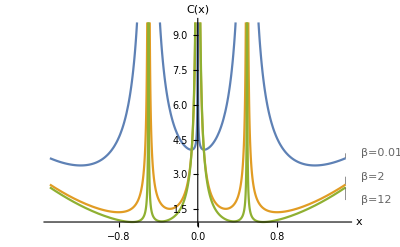

```mathematica
Plot[{c1[x],c2[x],c3[x]},{x,-1.5,1.5},PlotLabels->{"β=0.01","β=2","β=12"},AxesLabel->{x,"C(x)"}]
```

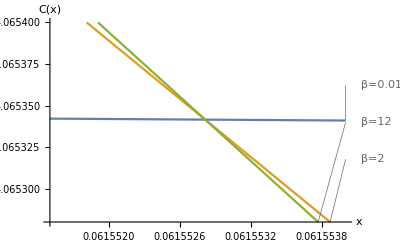

```mathematica
Plot[{c1[x],c2[x],c3[x]},{x,.0615515,0.061554},PlotLabels->{"β=0.01","β=2","β=12"},AxesLabel->{x,"C(x)"},PlotRange->{4.06528,4.0654}]
```